```mathematica
transfos={InfiniteLine[{{0,0},{1/2,(√3)/6}}],
InfiniteLine[{{1,0},{1/2,(√3)/6}}],
InfiniteLine[{{1/2,1},{1/2,0}}],
Arrow[Circle[{1/2,(√3)/6},0.2,{π/2,(7π)/6}]],
Arrow[Circle[{1/2,(√3)/6},0.15,{π/2,(11π)/6}]]};
```

```mathematica
triangle=
{{
Opacity[0.5],
Polygon[{
{0,0},
{1,0},
{1/2,(√3)/2}
}]},
{PointSize[Large],StandardRed,Point[{0,0}]},
{PointSize[Large],StandardGreen,Point[{1,0}]},
{PointSize[Large],StandardBlue,Point[{1/2,(√3)/2}]}
};
```

```mathematica
Graphics[{
transfos,triangle
}]
```

-Graphics-

```mathematica
Graphics[{
transfos,
Dynamic[GeometricTransformation[
triangle,
ScalingTransform[Clock[{-1,1},5,1],{1,0},{1/2,(√3)/6}]
]
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}}]
```

-Graphics-

```mathematica
s1[t_]:=ScalingTransform[2t-1,{-√3,3},{1/2,(√3)/6}]
```

```mathematica
s2[t_]:=ScalingTransform[2t-1,{√3,3},{1/2,(√3)/6}]
```

```mathematica
s3[t_]:=ScalingTransform[2t-1,{1,0},{1/2,(√3)/6}]
```

```mathematica
r1[t_]:=RotationTransform[(2π t)/3,{1/2,(√3)/6}]
```

```mathematica
r2[t_]:=RotationTransform[(4t π)/3,{1/2,(√3)/6}]
```

```mathematica
Graphics[{
transfos,
Dynamic[GeometricTransformation[triangle,r2[Clock[{0,1},5,1]]]
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}}]
```

-Graphics-

```mathematica
Clear[AnimateTransformations]
```

```mathematica
AnimateTransformations[transList_List,stepDur:5]:=Module[{n=Length[transList],duration},duration=stepDur*n;
Animate[
Graphics[
{
transfos,
Fold[
(GeometricTransformation[#1,#2]&),
triangle,
Table[transList[[i]][Min[1,Max[0,(t-(i-1)*stepDur)/stepDur]]],
{i,n}
]
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}}],
{t,0,duration},
AnimationRepetitions->1
]
];

AnimateTransformations[{s3,s2,r1},5]
```

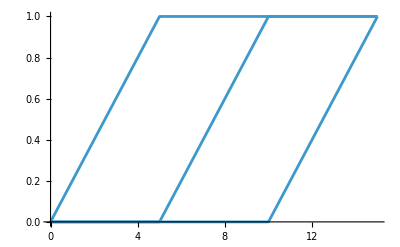

```mathematica
Plot[Table[{Min[1,Max[0,(t-(i-1)*5)/5]]},{i,3}],{t,0,15}]
```

```mathematica
transfos2={InfiniteLine[{{0,0},{1,1}}],
InfiniteLine[{{1,0},{0,1}}],
InfiniteLine[{{1/2,0},{1/2,1}}],
InfiniteLine[{{0,1/2},{1,1/2}}],
Arrow[Circle[{1/2,1/2},0.1,{(3π)/4,(5π)/4}]],
Arrow[Circle[{1/2,1/2},0.15,{(3π)/4,(7π)/4}]],
Arrow[Circle[{1/2,1/2},0.2,{(3π)/4,(9π)/4}]]
};
```

```mathematica
square=
{{
Opacity[0.5],
Polygon[{
{0,0},
{1,0},
{1,1},
{0,1}
}]},
{PointSize[Large],StandardRed,Point[{0,0}]},
{PointSize[Large],StandardGreen,Point[{1,0}]},
{PointSize[Large],StandardBlue,Point[{1,1}]},
{PointSize[Large],StandardYellow,Point[{0,1}]}
};
```

```mathematica
Graphics[{
transfos2,square
}]
```

-Graphics-

```mathematica
ss1[t_]:=ScalingTransform[2t-1,{1,0},{1/2,1/2}]
ss2[t_]:=ScalingTransform[2t-1,{1,1},{1/2,1/2}]
ss3[t_]:=ScalingTransform[2t-1,{0,1},{1/2,1/2}]
ss4[t_]:=ScalingTransform[2t-1,{-1,1},{1/2,1/2}]
```

```mathematica
sr1[t_]:=RotationTransform[(π t)/2,{1/2,1/2}]
sr2[t_]:=RotationTransform[π t,{1/2,1/2}]
sr3[t_]:=RotationTransform[(3π t)/2,{1/2,1/2}]
```

```mathematica
AnimateTransformationsSquare[transList_List,stepDur:5]:=Module[{n=Length[transList],duration},duration=stepDur*n;
Animate[
Graphics[
{
transfos2,
Fold[
(GeometricTransformation[#1,#2]&),
square,
Table[transList[[i]][Min[1,Max[0,(t-(i-1)*stepDur)/stepDur]]],
{i,n}
]
]
},
PlotRange->{{-0.1,1.1},{-0.1,1.1}}],
{t,0,duration},
AnimationRepetitions->1
]
];

AnimateTransformationsSquare[{ss1,ss3,sr2},5]
```